# Data Science and Machine Learning II

## Assignment 1: Green Domestic Product

In this assignment, you will calculate and explore the Green Domestic Product, an indicator developed by E4S that extends the scope of the GDP to integrate the depletion of natural, social, and human capital. In its current version, GrDP considers the impacts of the emissions of three groups of pollutants: greenhouse gases, air pollutants, heavy metals. These impacts include climate change, health issues, decrease in crops’ yields and biomass production, buildings degradation, and damages to ecosystems due to eutrophication. Read the new E4S white paper if you wish to learn more! You can also explore the results on the GrDP online dashboard. You will reproduce these results in this assignment. 

Once you are done you have to submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1213652 
There is no quiz, so your grade will depend only on your notebook.
If there is need for further clarifications on the questions, after the assignment is released, we will update this file, so make sure you check the git repository for updates.
	Good luck!

## Discover the dataset

Import as a dataset the CSV file: "GrDP_Data.csv".
You can directly Import from the GitHub link: https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_1/GrDP_Data.csv?token=GHSAT0AAAAAABYYLB5JXSIP2RWK3C5KAP3MYZISHIQ

```mathematica
dataset = Import["https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_1/GrDP_Data.csv?token=GHSAT0AAAAAABYYLB5JXSIP2RWK3C5KAP3MYZISHIQ", "Dataset", "HeaderLines" -> 1];
```

Question 1: 
Preview the dataset. Display a random sample of the dataset [1 point]

```mathematica
RandomSample[dataset,5]
```

Question 2: 
How many observations (rows) does the dataset contain? [1 point]

```mathematica
{nobs,ncol}=Dimensions[dataset]
```

{600,30}

Question 3: 
Extract the name of the columns to understand what information is displayed in the dataset [1 point]

```mathematica
keys=Normal@dataset[Keys][1]
```

{Country,Year,GDP [million Euro],Population,Emissions_GHG [thousand tonnes CO2eq],Emissions_NOx [tonne],Emissions_PM2.5 [tonne],Emissions_PM10 [tonne],Emissions_SOx [tonne],Emissions_NMVOC [tonne],Emissions_NH3 [tonne],Emissions_Pb [tonne],Emissions_Cd [tonne],Emissions_Hg [tonne],Emissions_As [tonne],Emissions_Ni [tonne],Emissions_Cr [tonne],Cost_GHG [Euro per tonnes CO2eq],Cost_NOx [Euro per tonne],Cost_PM2.5 [Euro per tonne],Cost_PM10 [Euro per tonne],Cost_SOx [Euro per tonne],Cost_NMVOC [Euro per tonne],Cost_NH3 [Euro per tonne],Cost_Pb [Euro per kg],Cost_Cd [Euro per kg],Cost_Hg [Euro per kg],Cost_As [Euro per kg],Cost_Ni [Euro per kg],Cost_Cr [Euro per kg]}

Question 4: 
What is the scope of countries? Years? [1 point]

```mathematica
country = DeleteDuplicates @dataset[All, "Country"] // Normal
```

{Belgium,Bulgaria,Czechia,Denmark,Germany,Estonia,Ireland,Greece,Spain,France,Croatia,Italy,Cyprus,Latvia,Lithuania,Luxembourg,Hungary,Malta,Netherlands,Austria,Poland,Portugal,Romania,Slovenia,Slovakia,Finland,Sweden,Norway,Switzerland,United Kingdom}

```mathematica
years = DeleteDuplicates @dataset[All, "Year"] // Normal
```

{2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019}

## Exploratory Data Analysis

Question 5: 
Plot the evolution of the emissions of NOx for the country of your choice [1 point]

```mathematica
noxSWE = Normal @ dataset[Select[#Country == "Sweden" &],"Emissions_NOx [tonne]"];
ts =  TimeSeries[noxSWE, {"2000", "2019"}];
DateListPlot[ts, PlotLabel -> "Evolution of NOx emission in Sweden [in tonnes]", PlotStyle ->Black]
```

-Graphics-

Question 6: 
Create a scatter plot of the natural logarithm of PM10 and GHG emissions (considering all countries and years). [1 point]

```mathematica
ListPlot[Log @Transpose @Normal@{dataset[All,"Emissions_PM10 [tonne]"],dataset[All,"Emissions_GHG [thousand tonnes CO2eq]"]},
                      PlotLabel -> "PM10 and GHG emissions",
                                         AxesLabel -> {"Log PM 10 emissions [tonne]","Log GHG emissions [thousand tonnes CO2eq]"}]
```

-Graphics-

Question 7:   
Compute the correlation matrix between GDP and the emissions of pollutants. Display the correlation matrix in a dataset where the rows and columns are labelled [1 point]

We fist compute the Correlation:

```mathematica
keyList = keys[[3;;17]];
corr = Correlation[Normal @ dataset[All, keyList][Values]];
```

To make your dataset clearer, you can remove the units of our variables. You can use StringDelete to remove the units. The second argument is the pattern. Here we remove everything in between brackets. "~~ ___ ~~" means any sequence of characters.

```mathematica
keyListNoUnit = StringDelete[#, "["~~___~~"]"]&[keyList]
```

{GDP ,Population,Emissions_GHG ,Emissions_NOx ,Emissions_PM2.5 ,Emissions_PM10 ,Emissions_SOx ,Emissions_NMVOC ,Emissions_NH3 ,Emissions_Pb ,Emissions_Cd ,Emissions_Hg ,Emissions_As ,Emissions_Ni ,Emissions_Cr }

We create our new dataset. Remember, a dataset is just a mix of lists and associations (when rows/columns are labelled).

```mathematica
Dataset @ AssociationThread[keyListNoUnit, Normal @ Transpose @Dataset @AssociationThread[keyListNoUnit,corr]]
```

We can also use MatrixPlot to get a nice visual:

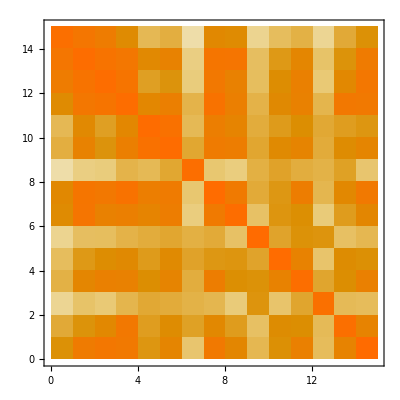

```mathematica
MatrixPlot[corr]
```

## Calculating GrDP

GrDP is defined as the GDP minus the external costs of pollutants.
The external costs of a given pollutant are calculated by multiplying the emissions by the marginal damage cost (unit cost).

Question 8: 
Compute the total external costs in million euros for all countries and years (be careful of units...) [1 point]

We create functions to calculate the external cost for each group of pollutants:

```mathematica
externalCostGHG[pol_]:= Normal @dataset[All,"Emissions_"<>pol<>" [thousand tonnes CO2eq]"] * Normal @dataset[All,"Cost_"<>pol<>" [Euro per tonnes CO2eq]"]/1000;
externalCostAP[pol_]:= Normal @dataset[All,"Emissions_"<>pol<>" [tonne]"] * Normal @dataset[All,"Cost_"<>pol<>" [Euro per tonne]"]/1000000;
externalCostHM[pol_]:= Normal @dataset[All,"Emissions_"<>pol<>" [tonne]"] * Normal @dataset[All,"Cost_"<>pol<>" [Euro per kg]"]/1000;
```

We will map these functions on the lists of pollutants:

```mathematica
listAP={"NOx","PM2.5", "PM10", "SOx","NMVOC", "NH3"};
listHM = {"Pb","Cd","Hg","As","Ni","Cr"};
```

We can finally compute the total external costs, as the sum of the cost of each group of pollutants:

```mathematica
totalExternalCost = externalCostGHG["GHG"] + Total[externalCostAP/@listAP] + Total[externalCostHM/@listHM];
```

Question 9 : 
Compute the share of external costs with respect to GDP in percentage [1 point]

```mathematica
shareExternalCost = totalExternalCost*100/ Normal@dataset[All, "GDP [million Euro]"];
```

Question 10: 
Compute the GrDP per capita in euros for all countries and years [1 point]

We first calculate GrDP = GDP - Total External Costs:

```mathematica
GrDP=Normal @dataset[All, "GDP [million Euro]"]-totalExternalCost;
```

The, GrDP per capita dividing by the population (since GrDP is in million euros, we multiply it by 1000000)

```mathematica
GrDPperCapita = GrDP*1000000/Normal @ dataset[All, "Population"];
```

Question 11: 
What are the share of external costs and GrDP per capita in Italy in 2005?  [1 point]

We first create a dataset that contains the external costs, the share of external cost, and the GrDP per capita.

```mathematica
dsResult = Transpose @Dataset @ AssociationThread[ {"External Cost","Share External Cost", "GrDP per capita"} ->{totalExternalCost,shareExternalCost,GrDPperCapita}] ;
```

We join our newly created dataset to the original one:

```mathematica
datasetResult = Join[dataset,dsResult,2];
```

Now we can easily select the country and year of our choice:

```mathematica
datasetResult[Select[#Country == "Italy" &&#Year ==2005 &],{"Share External Cost", "GrDP per capita"}]
```

## Visualizing the results

Question 12: 
Create a bar chart of the share of external costs for all countries in 2019, where the countries are sorted from lowest to highest share of external cost  [1 point]

We first create an association between our countries and the value of the share of external cost. We can easily Sort this association:

```mathematica
externalCost2019 = Sort @ AssociationThread[country,Normal @ datasetResult[Select[#Year ==2019 &],"Share External Cost"]]
```

<|Sweden→1.62249,Norway→2.70865,Switzerland→3.71869,Malta→3.86759,Finland→4.12211,Ireland→4.12641,Denmark→4.58113,Luxembourg→6.03166,Cyprus→7.06016,France→7.87669,United Kingdom→8.24634,Netherlands→8.25662,Austria→8.53004,Lithuania→9.18173,Germany→9.35663,Estonia→10.3419,Spain→11.0435,Belgium→12.2632,Portugal→17.5576,Italy→17.8423,Greece→18.1261,Latvia→19.9802,Slovakia→20.7621,Czechia→26.7383,Poland→27.172,Slovenia→27.5805,Hungary→29.7082,Croatia→35.0033,Romania→37.626,Bulgaria→54.7539|>

Now we can create our bar chart, applying some cool themes:

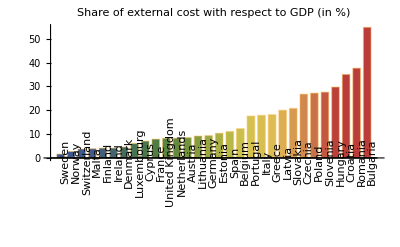

```mathematica
BarChart[externalCost2019, ChartStyle -> "DarkRainbow",
                         ChartLabels ->Placed[Keys[externalCost2019],Below, Rotate[#, Pi/2] &],
          PlotLabel -> "Share of external cost with respect to GDP (in %)"]
```

Question 13: 
Create a map of the GrDP per capita in 2019  [1 point]

We will make use of the power of entities! Let's first extract a list of our countries, as entities:

```mathematica
countryEntities = Interpreter["Country"][country];
```

We now create an association between our country as entity, and the value of GrDP per capita in 2019:

```mathematica
GrDPperCapita2019 = AssociationThread[countryEntities,Normal @ datasetResult[Select[#Year ==2019 &],"GrDP per capita"]];
```

Finally, we can create our map using GeoRegionValuePlot:

```mathematica
GeoRegionValuePlot[GrDPperCapita2019, ColorFunction -> "TemperatureMap", GeoProjection -> "Orthographic"]
```

-Graphics-

Question 14: 
Upgrade your previous map, adding an interactive feature allowing to select the year   [1 point]

We proceed as before, but this time we create a function that takes as input a year, and return an association between our country as entity, and the value of GrDP per capita in that given year:

```mathematica
GrDPperCapitaYear[y_]:=AssociationThread[countryEntities,Normal @ datasetResult[Select[#Year== y &],"GrDP per capita"]];
```

Now we can use Manipulate to create our interactive map:

```mathematica
Manipulate[GeoRegionValuePlot[GrDPperCapitaYear[i], ColorFunction -> "TemperatureMap"], {i, years}]
```

## Predicting GrDP...

Question 15: 
Build a linear regression model predicting GrDP per capita using the GDP, Population and all the emissions of pollutants. Split your dataset into training set and test set.  [1 point]

Let's first create a dataset keeping only the variables we will use for the regression:

```mathematica
regressKeys = Append[keyList,  "GrDP per capita"];
```

```mathematica
dataR = datasetResult[All, regressKeys];
```

Now we split our data into training and testing set:

```mathematica
{nobsR,ncolR}=Dimensions[dataR];
```

```mathematica
{trainingset,testset}=TakeDrop[RandomSample[dataR],Round[nobsR*0.8,1]];
```

We perform our linear regression:

```mathematica
pGrDP = Predict[trainingset ->"GrDP per capita", Method -> "LinearRegression"]
```

PredictorFunction[…]

We display the information of our predictor:

```mathematica
Information[pGrDP]
```

Predictor information
Data type | Mixed (number: 15)
Standard deviation | 14700. ± 1000.
Method | LinearRegression
Single evaluation time | 2.04 ms/example
Batch evaluation speed | 85.4 examples/ms
Loss | 11. ± 0.077
Model memory | 377. kB
Training examples used | 480 examples
Training time | 1.75 s
 |

Question 16: 
What are the L1 and L2 regularization coefficients of your predictor?  [1 point]

```mathematica
penaltyL1 = Information[pGrDP, "L1Regularization"]
penaltyL2 = Information[pGrDP, "L2Regularization"]
```

0

1.

Question 17: 
Assess the performance of your predictor on the test set. [1 point]

```mathematica
PredictorMeasurements[pGrDP, testset]
```

Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 120
Standard deviation | 14000. ± 1700.
Standard deviation baseline | 18500. ± 1800.
R-squared | 0.432 ± 0.17
Mean cross entropy | 11. ± 0.11
Single evaluation time | 2.61 ms/example
Batch evaluation speed | 1.71 examples/ms
-Graphics- |